## Visualization of square wave approximation using Fourier Series

### Introduction

Square wave is a periodic rectangular signal, widely used in radio engineering and electronics. Below is a graph of a square wave with a frequency of 5 Hz:

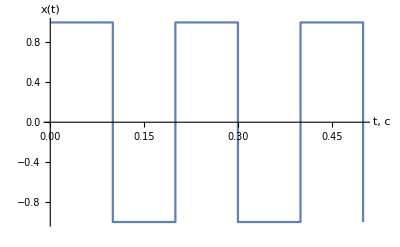

```mathematica
ListLinePlot[{{0.0,1},{0.1,1},{0.1,-1},{0.2,-1},{0.2,1},{0.3,1},{0.3,-1},{0.4,-1},{0.4,1},{0.5,1},{0.5,-1}},AxesLabel->{"t, с","x(t)"}]
```

Mathematically, a square wave can be described in many different ways, for example, through the signum function:

x(t)=sgn(sin(t))

The decomposition of a square wave with an amplitude of 1 and a frequency of f Hz into a Fourier series gives:

x(t)=4/π∑_(k=1)^∞ (sin(2π (2k-1))f t)/(2k-1)=4/π(sin(ω t)+1/3 sin(3ω t)+1/5 sin(5ω t)+…), where ω=2π f

Let’s plot the first 3 harmonics and their sums, as well as ∑_(n=1)^∞ x_n(t)=sgn(sin(2π t)):

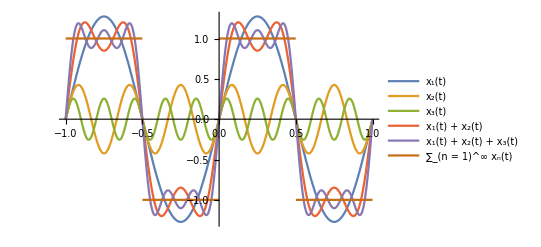

```mathematica
x1=(4 Sin[2π t])/π;
x2=(4 Sin[6π t])/(3 π);
x3=(4 Sin[10 π t])/(5 π);
Plot[{y1,y2,y3,y1+y2,y1+y2+y3,Sign[Sin[2π t]]},{t,-1,1},PlotLegends->{"x_1(t)", "x_2(t)","x_3(t)","x_1(t) + x_2(t)","x_1(t) + x_2(t) + x_3(t)","∑_(n = 1)^∞ x_n(t)"}]
```

The graph shows that increasing the number of terms in the series x(t) indeed gives a more accurate approximation.

For greater clarity, let’s create an animation in which each nth term of the series x(t) represented by a circle in polar coordinates.

### Code

```mathematica
ClearAll["Global`*"]
curveDistance=10;
curveStep=0.025;
curveWidthFactor=0.5;

GetX[t_,n_]:=Total@Table[((4 Cos[(2 k + 1) t])/((2 k + 1) Pi)),{k,0,n-1}];
GetY[t_,n_]:=Total@Table[((4 Sin[(2 k + 1) t])/((2 k + 1) Pi)),{k,0,n-1}];

MyCircle[x_,y_,r_,OptionsPattern[{Color->Black,Opacity->0.5}]]={OptionValue[Color],Opacity[OptionValue[Opacity]],Circle[{x,y},r]};
MyPoint[coords_,OptionsPattern[{Color->Black}]]:={OptionValue[Color],{PointSize[Medium],Point[coords]}};
MyLine[coords_,OptionsPattern[{Color->Black}]]:={OptionValue[Color],Line[coords]};
MyDashedLine[coords_,OptionsPattern[{Color->Black}]]:={OptionValue[Color],Dashed,Line[coords]};
MyCurve[t_,n_,OptionsPattern[{Color->Black}]]:=
{
OptionValue[Color],
Line[
MapThread[
List,
{
Table[-x*curveWidthFactor+curveDistance,{x,0,2 Pi,curveStep}],
Table[GetY[y,n],{y,t-2 Pi,t,curveStep}]
}
]
]
};
MySquareWave[t_,n_,OptionsPattern[{Color->Black}]]:=
{
OptionValue[Color],
Dotted,
Line[
MapThread[
List,
{
Table[-x*curveWidthFactor+curveDistance,{x,0,2 Pi,curveStep*4}],
Table[If[GetY[y,n]>0,1,-1],{y,t-2 Pi,t,curveStep*4}]
}
]
]
};
MyTransparentRectangle[{x0_,y0_},{x1_,y1_}]:=
{
Opacity[0.0],
Rectangle[{x0,y0},{x1,y1}]
}

frame[figures_List]:=Graphics[figures,Background->White];
GenerateFrame[t_,n_]:=Module[{figures,i,a,r},
figures={};

For[i=0,i<n,i++,
r=(4/((2 i + 1) Pi));
AppendTo[figures,MyCircle[GetX[t,i],GetY[t,i],r, Opacity->0.25]];
];

AppendTo[figures,MyLine[Insert[Table[{GetX[t,i],GetY[t,i]},{i,0,n}],{0,0},1]]];
AppendTo[figures,MyCurve[t,n]];
AppendTo[figures,MySquareWave[t,n]];
AppendTo[figures,MyDashedLine[{{GetX[t,n],GetY[t,n]},{curveDistance- 2*curveWidthFactor*Pi,GetY[t,n]}}]];
AppendTo[figures,MyPoint[{curveDistance-2*curveWidthFactor*Pi,GetY[t,n]}, Color->Red]];
AppendTo[figures,MyPoint[{GetX[t,n],GetY[t,n]},Color->Red]];
AppendTo[figures,MyTransparentRectangle[{GetX[0,n],2},{GetX[π,n],-2}]];

frame[figures]
];

GenerateFrames[n_]:=Table[GenerateFrame[t,n],{t,0,2 Pi-0.001,Pi/128}];
```

### Calculation of animations for different numbers (n) of Fourier series terms

```mathematica
n1=GenerateFrames[1];
n2=GenerateFrames[2];
n5=GenerateFrames[5];
n10=GenerateFrames[10];
n20=GenerateFrames[20];
```

### Results

n=1

```mathematica
ListAnimate[n1,ImageSize->Large,AnimationRunning->False]
```

n=2

```mathematica
ListAnimate[n2,ImageSize->Large,AnimationRunning->False]
```

n=5

```mathematica
ListAnimate[n5,ImageSize->Large,AnimationRunning->False]
```

n=10

```mathematica
ListAnimate[n10,ImageSize->Large,AnimationRunning->False]
```

n=20

```mathematica
ListAnimate[n20,ImageSize->Large,AnimationRunning->False]
```